Set Input Folder, Output Folder, Specific Folder, Number of Channels, Number of Runs:

```mathematica
OutputFolder="C:\\Users\\Karen\\Research\\60Fe\\Activity Measurement\\Planar\\Analysis\\";
InputFolder= "C:\\Users\\Karen\\Research\\60Fe\\Activity Measurement\\Planar\\2014\\";
SpecificFolder="May23\\";
NumberChannelAway=512;
NumberChannelNear=4096;
NumberRunAway=71;
NumberRunNear=71;
```

Definition of Gaussian Function:

```mathematica
Gaussian[x_,sig_,center_,Cmax_]:=Cmax 1/(sig √(2π))Exp[(-(x-center)^2)/(2 sig^2)];
```

Names of Files for Calibration:

```mathematica
CalibrationN="CALNEAR.DAT";
CalibrationA="CALAWAY.DAT";
```

241Am (+ 60Co) Calibration:

```mathematica
CalAway=Import[InputFolder<>SpecificFolder<>CalibrationA,"Table"];
CalNear=Import[InputFolder<>SpecificFolder<>CalibrationN,"Table"];
DataCalA=Drop[CalAway, 10];
InfoCalA=Drop[CalAway,-NumberChannelAway];
DataCalN=Drop[CalNear, 10];
InfoCalN=Drop[CalNear, -NumberChannelNear];
```

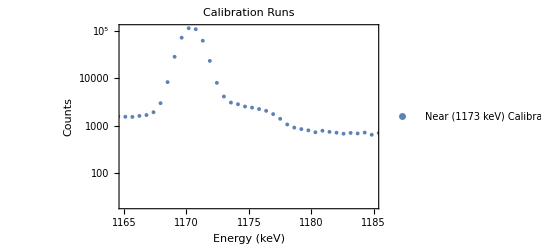

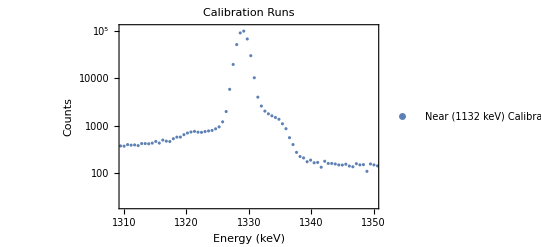

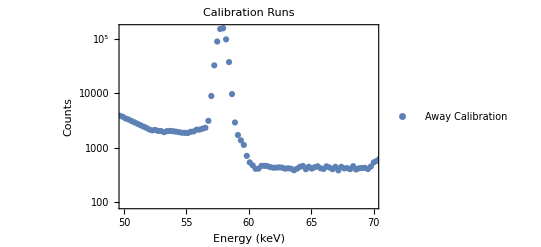

```mathematica
ListLogPlot[Table[{DataCalN[[i,2]],DataCalN[[i,3]]},{i,1,NumberChannelNear}],
Joined->False,
Frame->True,
FrameLabel->{Text[Style["Energy (keV)", FontSize->14]],Text[Style["Counts",FontSize->14]]},
PlotLabel->"Calibration Runs",
PlotLegends->{ "Near (1173 keV) Calibration"},
PlotRange->{{1165, 1185},All}]
ListLogPlot[Table[{DataCalN[[i,2]],DataCalN[[i,3]]},{i,1,NumberChannelNear}],
Joined->False,
Frame->True,
FrameLabel->{Text[Style["Energy (keV)", FontSize->14]],Text[Style["Counts",FontSize->14]]},
PlotLabel->"Calibration Runs",
PlotLegends->{ "Near (1132 keV) Calibration"},
PlotRange->{{1310, 1350},All}]
ListLogPlot[Table[{DataCalA[[i,2]],DataCalA[[i,3]]},{i,1,NumberChannelAway}],
 Joined->False,
 Frame->True, 
FrameLabel->{Text[Style["Energy (keV)", FontSize->14]],
Text[Style["Counts",FontSize->14]]},
PlotLabel->"Calibration Runs",
PlotLegends->{ "Away Calibration"},
PlotRange->{{50,70},All}]
```

Away Fitting:

```mathematica
FitCalA=ConstantArray[0,{NumberChannelAway,2}];
FitCalA[[All,1]]=DataCalA[[All,2]];
FitCalA[[All,2]]=DataCalA[[All,3]];
FitCalASmall=Select[FitCalA, #[[1]]>50 &];
FitCalASmall2=Select[FitCalASmall, #[[1]]<70 &];
MaximumA=Max[FitCalASmall2[[All,2]]]
MaximumPositionA=Position[FitCalASmall2, MaximumA][[1,1]];
MaximumXA=FitCalASmall2[[MaximumPositionA,1]]
```

157795

57.94

```mathematica
FindFit[FitCalASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXA},{sigma,2},{cmax,MaximumA}},x];
XoCalA=FindFit[FitCalASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXA},{sigma,2},{cmax,MaximumA}},x][[1,2]]
SigmaCalA=FindFit[FitCalASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXA},{sigma,2},{cmax,MaximumA}},x][[2,2]]
CMaxCalA=FindFit[FitCalASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXA},{sigma,2},{cmax,MaximumA}},x][[3,2]]
```

57.8353

0.33744

139575.

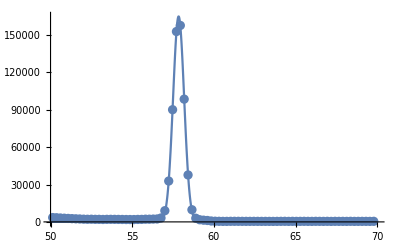

```mathematica
MyPlot=Plot[Gaussian[x,SigmaCalA,XoCalA,CMaxCalA],{x,50,70},PlotRange->{{50, 70}, All}];
Show[{MyPlot,ListPlot[FitCalASmall2]}]
```

Near Fitting:

```mathematica
FitCalN=ConstantArray[0,{NumberChannelNear,2}];
FitCalN[[All,1]]=DataCalN[[All,2]];
FitCalN[[All,2]]=DataCalN[[All,3]];
FitCalNSmall=Select[FitCalN, #[[1]]>1160.0 &];
FitCalNSmall2=Select[FitCalNSmall, #[[1]]<1190.0 &];
MaximumN=Max[FitCalNSmall2[[All,2]]]
MaximumPositionN=Position[FitCalNSmall2, MaximumN][[1,1]];
MaximumXN=FitCalNSmall2[[MaximumPositionN,1]]
```

115378

1170.18

```mathematica
FindFit[FitCalNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXN},{sigma,2},{cmax,MaximumN}},x];
XoCalN=FindFit[FitCalNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXN},{sigma,2},{cmax,MaximumN}},x][[1,2]]
SigmaCalN=FindFit[FitCalNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXN},{sigma,2},{cmax,MaximumN}},x][[2,2]]
CMaxCalN=FindFit[FitCalNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXN},{sigma,2},{cmax,MaximumN}},x][[3,2]]
```

1170.41

0.809239

241954.

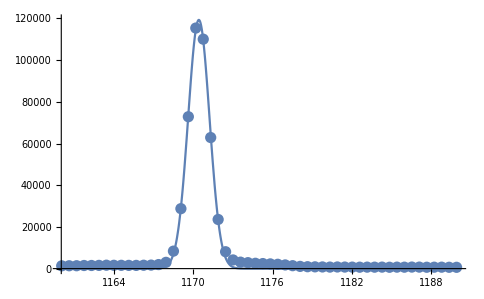

```mathematica
MyPlot=Plot[Gaussian[x,SigmaCalN,XoCalN,CMaxCalN],{x,1160,1190},PlotRange->{{1160, 1190}, All}];
Show[{MyPlot,ListPlot[FitCalNSmall2]}]
```

Results:

```mathematica
CalTimeA=InfoCalA[[2,5]] "seconds = Away time"
SigmaCalA "keV = Away Sigma"
MaximumXA "keV = Away Energy of Max"
CalTimeN=InfoCalN[[2,5]] "seconds = Near time"
SigmaCalN "keV = Near Sigma"
MaximumXN "keV = Near Energy of Max"
```

7200 seconds = Away time

0.33744 keV = Away Sigma

57.94 keV = Away Energy of Max

7200 seconds = Near time

0.809239 keV = Near Sigma

1170.18 keV = Near Energy of Max

External Notebooks for Functions and outputted Numbers:

```mathematica
outputs = NotebookOpen["C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/Analysis/Outputs.nb"];
```

```mathematica
nb1 = NotebookOpen["C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/Analysis/PeakInfoCout.nb"];
SelectionMove[nb1, All, Notebook]
NotebookEvaluate[nb1]
NotebookClose[nb1]
```

```mathematica
nb3 = NotebookOpen["C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/Analysis/PeakGraph.nb"];
SelectionMove[nb3, All, Notebook]
NotebookEvaluate[nb3]
NotebookClose[nb3]
```

Away Detector

```mathematica
LastRunNumber=71;
```

```mathematica
Do[
ToExpression["ISOA"<>ToString[i]<>"=Import[InputFolder<>SpecificFolder<>\"ISOA"<>ToString[i]<>".DAT\", \"Table\"]"],
{i,0,LastRunNumber}]
Do[
ToExpression["ISOA"<>ToString[i]<>"d=Drop[ISOA"<>ToString[i]<>",10];"];
ToExpression["ISOA"<>ToString[i]<>"b=Drop[ISOA"<>ToString[i]<>",-NumberChannelAway];"];,
{i,0,LastRunNumber}]
```

```mathematica
Do[ToExpression["ISOA"<>ToString[i]<>"=Import[InputFolder<>SpecificFolder<>\"ISOA"<>ToString[i]<>".DAT\", \"Table\"]"],{i,0,LastRunNumber}]
```

```mathematica
Awaylist=ConstantArray[0,{NumberChannelAway,LastRunNumber+3}];(*Makes an array for all of the runs.*)
Awaylist[[All, 1]]=ISOA0d[[All,1]] ;(*First column is channel number. *)
Awaylist[[All,2]]=ISOA0d[[All,2]]; (*Second column is energy in keV.*)
Do[
ToExpression["Awaylist[[All,"<>ToString[i+3]<>"]]=ISOA"<>ToString[i]<>"d[[All,3]];"],
{i,0,LastRunNumber}]; (* All of the remaining columns except the last one are the number of counts from the runs in that channel.*)
Awaylist[[All,LastRunNumber+3]]=Sum[Awaylist[[All,i]],{i,3,LastRunNumber+2}];(*The last column is a sum of the previous columns, a total number of counts in that channel.*)
(*This remakes the list to include only the energy and the total number of counts, column 2 and 27.*)
Awaylistfinal=ConstantArray[0,{NumberChannelAway,2}];
Awaylistfinal[[All,1]]=Awaylist[[All,2]];
Awaylistfinal[[All,2]]=Awaylist[[All,LastRunNumber+3]];
Awaylistfinal//MatrixForm;
```

```mathematica
TimeA=0;
For[i=0,i<LastRunNumber+1, i++, ToExpression["TimeA=TimeA + ISOA"<>ToString[i]<>"b[[2,5]]"]]
TimeA
```

513093

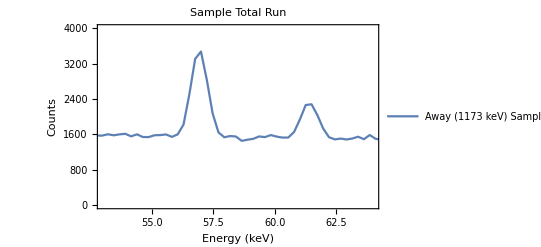

```mathematica
ListPlot[Table[{Awaylistfinal[[i,1]],Awaylistfinal[[i,2]]},{i,1,NumberChannelAway}],
Joined->True,
Frame->True,
FrameLabel->{Text[Style["Energy (keV)", FontSize->14]],Text[Style["Counts",FontSize->14]]},
PlotLabel->"Sample Total Run",
PlotLegends->{"Away (1173 keV) Sample"},
PlotRange->{{53, 64},{0, 4000}}]
```

Sample Away Fitting:

```mathematica
FitSamplelASmall=Select[Awaylistfinal, #[[1]]>56 &];
FitSamplelASmall2=Select[FitSamplelASmall, #[[1]]< 58&];
MaximumSampleA=Max[FitSamplelASmall2[[All,2]]]
MaximumPositionSampleA=Position[FitSamplelASmall2, MaximumSampleA][[1,1]];
MaximumXSampleA=FitSamplelASmall2[[MaximumPositionSampleA,1]]
```

3473

56.993

```mathematica
FindFit[FitSamplelASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleA},{sigma,2},{cmax,MaximumSampleA}},x];
XoSampleA=FindFit[FitSamplelASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleA},{sigma,2},{cmax,MaximumSampleA}},x][[1,2]]
SigmaSampleA=FindFit[FitSamplelASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleA},{sigma,2},{cmax,MaximumSampleA}},x][[2,2]]
CMaxSampleA=FindFit[FitSamplelASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleA},{sigma,2},{cmax,MaximumSampleA}},x][[3,2]]
```

56.9385

0.701034

5620.52

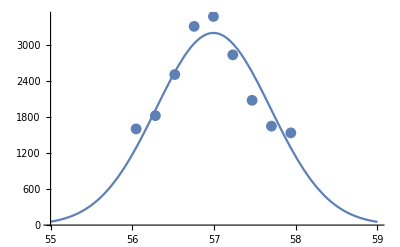

```mathematica
MyPlot=Plot[Gaussian[x,SigmaSampleA,MaximumXSampleA,CMaxSampleA],{x,55, 59},PlotRange->All];
Show[{MyPlot,ListPlot[
FitSamplelASmall2]}]
```

Near Detector

```mathematica
Do[
ToExpression["ISON"<>ToString[i]<>"=Import[InputFolder<>SpecificFolder<>\"ISON"<>ToString[i]<>".DAT\", \"Table\"]"],
{i,0,LastRunNumber}]
Do[
ToExpression["ISON"<>ToString[i]<>"d=Drop[ISON"<>ToString[i]<>",10];"];
ToExpression["ISON"<>ToString[i]<>"b=Drop[ISON"<>ToString[i]<>",-NumberChannelNear];"];,
{i,0,LastRunNumber}]
```

```mathematica
Nearlist=ConstantArray[0,{NumberChannelNear,LastRunNumber+3}];(*Makes an array for all of the runs.*)
Nearlist[[All, 1]]=ISON0d[[All,1]];(*First column is channel number. *)
Nearlist[[All,2]]=ISON0d[[All,2]]; (*Second column is energy in keV.*)
Do[
ToExpression["Nearlist[[All,"<>ToString[i+3]<>"]]=ISON"<>ToString[i]<>"d[[All,3]];"],
{i,0,LastRunNumber}]; (* All of the remaining columns except the last one are the number of counts from the runs in that channel.*)
Nearlist[[All,LastRunNumber+3]]=Sum[Nearlist[[All,i]],{i,3,LastRunNumber+2}];(*The last column is a sum of the previous columns, a total number of counts in that channel.*)
(*This remakes the list to include only the energy and the total number of counts, column 2 and 27.*)
Nearlistfinal=ConstantArray[0,{NumberChannelNear,2}];
Nearlistfinal[[All,1]]=Nearlist[[All,2]];
Nearlistfinal[[All,2]]=Nearlist[[All,LastRunNumber+3]];
```

```mathematica
TimeN=0;
For[i=0,i<LastRunNumber+1, i++, ToExpression["TimeN=TimeN + ISON"<>ToString[i]<>"b[[2,5]]"]]
TimeN
```

511058

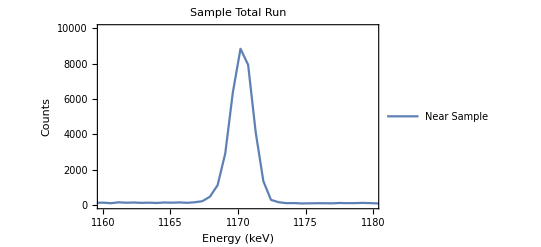

```mathematica
ListPlot[Table[{Nearlistfinal[[i,1]],Nearlistfinal[[i,2]]},{i,1,NumberChannelNear}],
Joined->True,
Frame->True,
FrameLabel->{Text[Style["Energy (keV)", FontSize->14]],Text[Style["Counts",FontSize->14]]},
PlotLabel->"Sample Total Run",
PlotLegends->{"Near Sample"},
PlotRange->{{1160,1180}, {0,10000}}]
```

Sample Near Fitting:

```mathematica
FitSamplelNSmall=Select[Nearlistfinal, #[[1]]>1167 &];
FitSamplelNSmall2=Select[FitSamplelNSmall, #[[1]]<1173 &];
MaximumSampleN=Max[FitSamplelNSmall2[[All,2]]]
MaximumPositionSampleN=Position[FitSamplelNSmall2, MaximumSampleN][[1,1]];
MaximumXSampleN=FitSamplelNSmall2[[MaximumPositionSampleN,1]]
```

8839

1170.18

```mathematica
FindFit[FitSamplelNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleN},{sigma,.5},{cmax,MaximumSampleN}},x];
XoSampleN=FindFit[FitSamplelNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleN},{sigma,.5},{cmax,MaximumSampleN}},x][[1,2]]
SigmaSampleN=FindFit[FitSamplelNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleN},{sigma,.5},{cmax,MaximumSampleN}},x][[2,2]]
CMaxSampleN=FindFit[FitSamplelNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXSampleN},{sigma,.5},{cmax,MaximumSampleN}},x][[3,2]]
```

1170.29

0.830434

18685.7

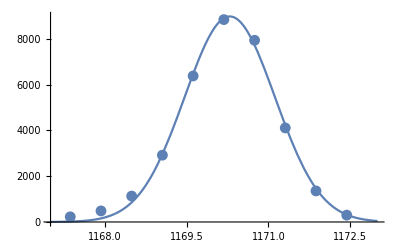

```mathematica
MyPlot=Plot[Gaussian[x,SigmaSampleN,XoSampleN,CMaxSampleN],{x,1167,1173},PlotRange->All];
Show[{MyPlot,ListPlot[FitSamplelNSmall2]}]
```

Results for Sample:

```mathematica
TimeA "seconds = Away time"
SigmaSampleA "keV = Away Sigma"
MaximumXSampleA "keV = Away Energy of Max"
TimeN "seconds = Near time"
SigmaSampleN "keV = Near Sigma"
MaximumXSampleN "keV = Near Energy of Max"
```

510264 seconds = Away time

0.701034 keV = Away Sigma

56.993 keV = Away Energy of Max

511058 seconds = Near time

0.830434 keV = Near Sigma

1170.18 keV = Near Energy of Max

```mathematica
Background
```

```mathematica
BackRunNumber=11;
AwayChannels=512;
NearChannels=4096;
```

```mathematica
Do[
ToExpression["BackISOA"<>ToString[i]<>"=Import[\"C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/2016/Dec19/ISOA"<>ToString[i]<>".dat\", \"Table\"];"],
{i,0,BackRunNumber}];
Do[
ToExpression["BackISOA"<>ToString[i]<>"d=Drop[BackISOA"<>ToString[i]<>",10];"];
ToExpression["BackISOA"<>ToString[i]<>"b=Drop[BackISOA"<>ToString[i]<>",-512];"];,
{i,0,BackRunNumber}]
```

```mathematica
Do[
ToExpression["BackISON"<>ToString[i]<>"=Import[\"C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/2016/Dec19/ISON"<>ToString[i]<>".dat\", \"Table\"];"],
{i,0,BackRunNumber}];
Do[
ToExpression["BackISON"<>ToString[i]<>"d=Drop[BackISON"<>ToString[i]<>",10];"];
ToExpression["BackISON"<>ToString[i]<>"b=Drop[BackISON"<>ToString[i]<>",-512];"];,
{i,0,BackRunNumber}]
```

```mathematica
BackAwaylist=ConstantArray[0,{AwayChannels,BackRunNumber+3}]; (*Makes an array for all of the runs.*)
BackAwaylist[[All, 1]]=BackISOA0d[[All,1]];(*First column is channel number. *)
BackAwaylist[[All,2]]=BackISOA0d[[All,2]];(*Second column is energy in keV.*)
Do[
ToExpression["BackAwaylist[[All,"<>ToString[i+3]<>"]]=BackISOA"<>ToString[i]<>"d[[All,3]];"],
{i,0,BackRunNumber}]; (* All of the remaining columns except the last one are the number of counts from the runs in that channel.*)
BackAwaylist[[All,BackRunNumber+3]]=Sum[BackAwaylist[[All,i]],{i,3,BackRunNumber+2}]; (*The last column is a sum of the previous columns, a total number of counts in that channel.*)
(*This remakes the list to include only the energy and the total number of counts, column 2 and 27.*)
BackAwaylistfinal=ConstantArray[0,{AwayChannels,2}];
BackAwaylistfinal[[All,1]]=BackAwaylist[[All,2]];
BackAwaylistfinal[[All,2]]=BackAwaylist[[All,BackRunNumber+3]];
```

```mathematica
BackNearlist=ConstantArray[0,{NearChannels,BackRunNumber+3}]; (*Makes an array for all of the runs.*)
BackNearlist[[All, 1]]=BackISON0d[[All,1]]; (*First column is channel number. *)
BackNearlist[[All,2]]=BackISON0d[[All,2]]; (*Second column is energy in keV.*)
Do[
ToExpression["BackNearlist[[All,"<>ToString[i+3]<>"]]=BackISON"<>ToString[i]<>"d[[All,3]];"],
{i,0,BackRunNumber}]; (* All of the remaining columns except the last one are the number of counts from the runs in that channel.*)
BackNearlist[[All,BackRunNumber+3]]=Sum[BackNearlist[[All,i]],{i,3,BackRunNumber+2}]; (*The last column is a sum of the previous columns, a total number of counts in that channel.*)
(*This remakes the list to include only the energy and the total number of counts, column 2 and 27.*)
BackNearlistfinal=ConstantArray[0,{NearChannels,2}];
BackNearlistfinal[[All,1]]=BackNearlist[[All,2]];
BackNearlistfinal[[All,2]]=BackNearlist[[All,BackRunNumber+3]];
```

```mathematica
BackTimeA=0;
For[i=0,i<BackRunNumber, i++, ToExpression["BackTimeA=  BackTimeA + BackISOA"<>ToString[i]<>"b[[2,5]]"]]
BackTimeA
BackTimeN=0;
For[i=0,i<BackRunNumber, i++, ToExpression["BackTimeN=  BackTimeN + BackISON"<>ToString[i]<>"b[[2,5]]"]]
BackTimeN
```

79133

79189

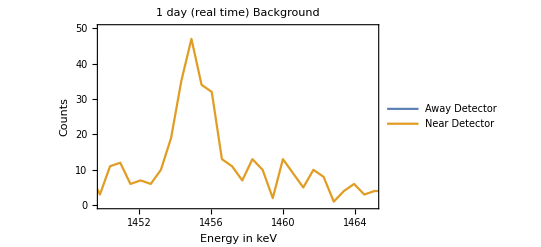

```mathematica
ListPlot[{Table[{BackAwaylist[[i,2]], BackAwaylist[[i,BackRunNumber+3]]}, {i, 1, AwayChannels}], Table[{BackNearlist[[i,2]], BackNearlist[[i,BackRunNumber+3]]},{i,1, NearChannels}]},
Joined->True,
InterpolationOrder->1,
FrameLabel->{Text[Style["Energy in keV", FontSize->14]],Text[Style["Counts", FontSize->14]]},
PlotLabel->"1 day (real time) Background",
Frame->True,
PlotLegends->{"Away Detector", "Near Detector"},
PlotRange->{{1450, 1465},{0,50}}
]
```

Background Away Fitting:

```mathematica
FitBackASmall=Select[BackAwaylistfinal, #[[1]]>60.5 &];
FitBackASmall2=Select[FitBackASmall, #[[1]]<62.5 &];
MaximumBackA=Max[FitBackASmall2[[All,2]]]
MaximumPositionBackA=Position[FitBackASmall2, MaximumBackA][[1,1]];
MaximumXBackA=FitBackASmall2[[MaximumPositionBackA,1]]
```

184

61.253

```mathematica
FindFit[FitBackASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackA},{sigma,2},{cmax,MaximumBackA}},x];
XoBackA=FindFit[FitBackASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackA},{sigma,2},{cmax,MaximumBackA}},x][[1,2]]
SigmaBackA=FindFit[FitBackASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackA},{sigma,2},{cmax,MaximumBackA}},x][[2,2]]
CMaxBackA=FindFit[FitBackASmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackA},{sigma,2},{cmax,MaximumBackA}},x][[3,2]]
```

61.3742

0.473531

197.838

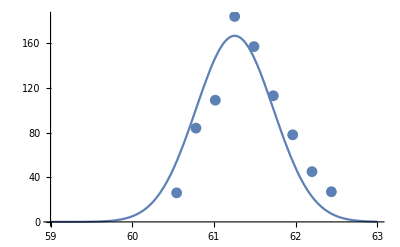

```mathematica
MyPlot=Plot[Gaussian[x,SigmaBackA,MaximumXBackA,CMaxBackA],{x,59,63},PlotRange->All];
Show[{MyPlot,ListPlot[FitBackASmall2]}]
```

Background Near Fitting:

```mathematica
FitBackNSmall=Select[BackNearlistfinal, #[[1]]>1452&];
FitBackNSmall2=Select[FitBackNSmall, #[[1]]<1457.5 &];
MaximumBackN=Max[FitBackNSmall2[[All,2]]]
MaximumPositionBackN=Position[FitBackNSmall2, MaximumBackN][[1,1]];
MaximumXBackN=FitBackNSmall2[[MaximumPositionBackN,1]]
```

47

1454.92

```mathematica
FindFit[FitBackNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackN},{sigma,2},{cmax,MaximumBackN}},x];
XoBackN=FindFit[FitBackNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackN},{sigma,2},{cmax,MaximumBackN}},x][[1,2]]
SigmaBackN=FindFit[FitBackNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackN},{sigma,2},{cmax,MaximumBackN}},x][[2,2]]
CMaxBackN=FindFit[FitBackNSmall2, Gaussian[x,sigma,x0,cmax],{{x0,MaximumXBackN},{sigma,2},{cmax,MaximumBackN}},x][[3,2]]
```

1455.06

1.12185

119.038

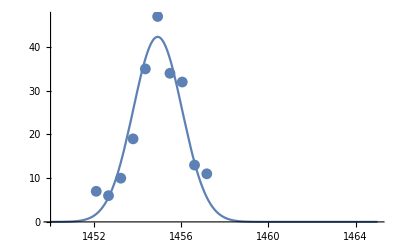

```mathematica
MyPlot=Plot[Gaussian[x,SigmaBackN,MaximumXBackN,CMaxBackN],{x,1450,1465},PlotRange->All];
Show[{MyPlot,ListPlot[FitBackNSmall2]}]
```

```mathematica
Export["C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/Analysis/Jun17and18.png",ListPlot[{Table[{Awaylistfinal[[i,1]], Awaylistfinal[[i,2]]}, {i, 1, AwayChannels}], Table[{BackAwaylist[[i,2]], BackAwaylist[[i,BackRunNumber+3]]},{i,1, NearChannels}]},
Joined->True,
InterpolationOrder->0,
FrameLabel->{Text[Style["Energy in keV", FontSize->14]],Text[Style["Counts", FontSize->14]]},
PlotLabel->"1 day (real time) Run",
Frame->True,
PlotLegends->Placed[SwatchLegend[{Blue, Orange},{"'Fe-1' Sample", "Background"}],Below],
PlotRange->{{55, 66},{0,250}}]]
```

C:/Users/Karen/Research/60Fe/Activity Measurement/Planar/Analysis/Jun17and18.png